```mathematica
(*
This notebook executes the computations needed to present the lift of the Deligne-Mostow lattice (11,7,2,2,2)/12 to the universal cover of SU(2,1).

The lift of the DM lattice to SU(2,1) will have generators b,u,v subject to the relations {b^3, u^3, v^4, b*v=v*b, u*b*u=b*u*b, (u*v)^2=(v*u)^2, (b*u*v)^3}.

Our lifts of these elements to the universal cover will be {B,U,V}.

The element of the universal cover of SU(2,1) mapping to a generator for the center <E^(2*Pi*I/3)*Id> of SU(2,1) will be denoted z.
Then z^3 is a generator for the universal cover of SU(2,1).

The presentation we find has relations
{B^3*z, U^3*z, V^6*z, B*V=V*B, U*B*U=B*U*B, (U*V)^2=(V*U)^2, (B*U*V)^3*z^3}
*)
```

```mathematica
(* The standard hermitian form *)
h0 = {{0,0,1},{0,1,0},{1,0,0}};
```

```mathematica
(* The vector whose orbit is the our circle bundle over the ball *)
z0 = {-1,0,1};
```

```mathematica
(* Projection onto the third coordinate *)
p3 ={0,0,1};
```

```mathematica
(* The hermitian form for the natural generators *)
h={{1+Sqrt[3],-1,0},{-1,-1+Sqrt[3],0},{0,0,-1}};
```

```mathematica
(* Natural generators *)
v0={{I,0,0},{(-1/2+I/2)*(1+Sqrt[3]),1,0},{0,0,1}}//ComplexExpand//FullSimplify;
u0={{(1/2+I/2)*(1+Sqrt[-3]),1-(-1)^(1/6),0},{(I/2)*(2+I+Sqrt[3]),-(-1)^(5/6),0},{0,0,1}}//ComplexExpand//FullSimplify;
b0={{1,0,0},{Sqrt[3]*(1-I/2)+3/2-I,(-1/2+I/2)*(1+Sqrt[3]),-(I/2)*(2-I+Sqrt[3])},{(1/2+I/2)*(1+Sqrt[3]),-1-I,(1/2)*(2-I+Sqrt[3])}}//ComplexExpand//FullSimplify;
```

```mathematica
(* The elements b0,u0,v0 are lifts from PU(2,1) to U(2,1), so we scale to get lifts to SU(2,1) *)
v1=Det[v0]^(-1/3)*v0//ComplexExpand//FullSimplify;
u1=Det[u0]^(-1/3)*u0//ComplexExpand//FullSimplify;
b1=Det[b0]^(-1/3)*b0//ComplexExpand//FullSimplify;
```

```mathematica
Det[b1]//FullSimplify
Det[u1]//FullSimplify
Det[v1]//FullSimplify
```

1

1

1

```mathematica
(* The power relations - b1, u1, and v1 have powers that are E^(4*Pi*I)*Id, whereas (b1*u1*v1)^3=Id, and recall that E^(4*Pi*I)*Id is a generator for the center of SU(2,1) *)
MatrixPower[v1,4]-E^(4*Pi*I/3)*{{1,0,0},{0,1,0},{0,0,1}}//ComplexExpand//FullSimplify//MatrixForm
MatrixPower[u1,3]-E^(4*Pi*I/3)*{{1,0,0},{0,1,0},{0,0,1}}//ComplexExpand//FullSimplify//MatrixForm
MatrixPower[b1,3]-E^(4*Pi*I/3)*{{1,0,0},{0,1,0},{0,0,1}}//ComplexExpand//FullSimplify//MatrixForm
MatrixPower[b1.u1.v1,3]//ComplexExpand//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(* Checking that b1,u1,v1 preserve our hermitian form *)
Conjugate[Transpose[b1]].h.b1-h//FullSimplify
Conjugate[Transpose[u1]].h.u1-h//FullSimplify
Conjugate[Transpose[v1]].h.v1-h//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* Braid relations all lift to SU(2,1) *)
b1.v1-v1.b1//FullSimplify
u1.b1.u1-b1.u1.b1//FullSimplify
u1.v1.u1.v1-v1.u1.v1.u1//FullSimplify
```

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
(* We now convert h to h0 and conjugate our generators appropriately *)
c1={{(1+Sqrt[3])^(-1/2),(1+Sqrt[3])^(-1/2),0},{0,(1+Sqrt[3])^(1/2),0},{0,0,1}};
d1=Inverse[c1]//FullSimplify;
c2={{1/Sqrt[2],0,1/Sqrt[2]},{0,1,0},{-1/Sqrt[2],0,1/Sqrt[2]}};
c=c1.c2//FullSimplify;
d=Inverse[c]//FullSimplify;
h0-Transpose[c].h.c//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(* Our converted generators *)
v=d.v1.c//ComplexExpand//FullSimplify;
u=d.u1.c//ComplexExpand//FullSimplify;
b=d.b1.c//ComplexExpand//FullSimplify;
```

```mathematica
(* Check that our generators indeed preserve the correct form *)
Conjugate[Transpose[v]].h0.v-h0//ComplexExpand//FullSimplify//MatrixForm
Conjugate[Transpose[u]].h0.u-h0//ComplexExpand//FullSimplify//MatrixForm
Conjugate[Transpose[b]].h0.b-h0//ComplexExpand//FullSimplify//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(* Matrix logarithm so we can define paths from Id to each generator *)
xb = MatrixLog[N[b,25]];
xu = MatrixLog[N[u,25]];
xv = MatrixLog[N[v,25]];
```

```mathematica
(* Remark: In the notation at the beginning of this document, z represents counterclockwise rotation by Pi/3, since z^3 generates the fundamental group of SU(2,1) *)
```

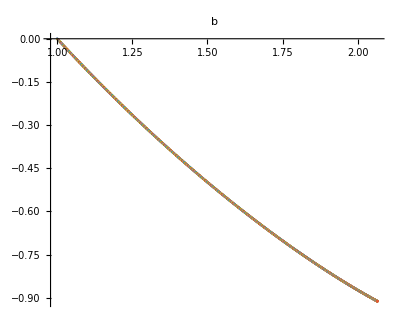

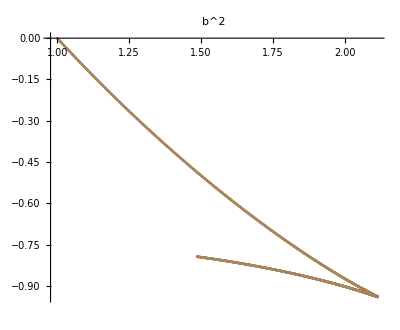

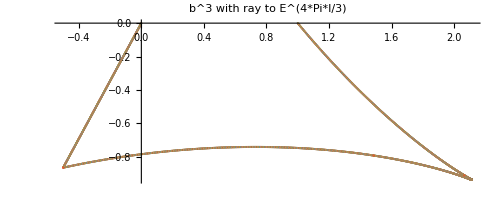

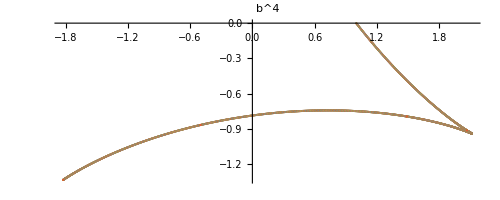

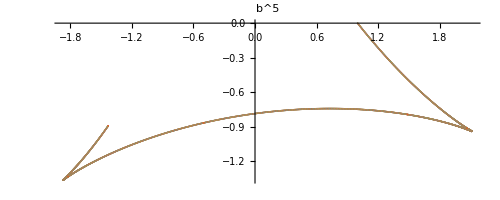

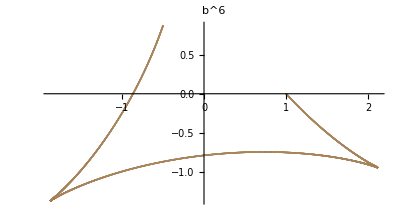

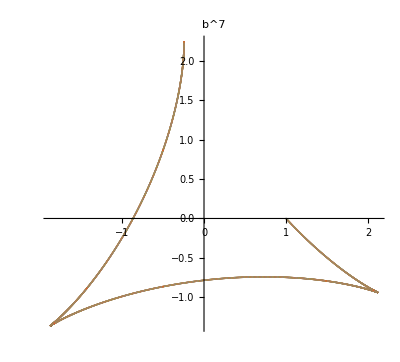

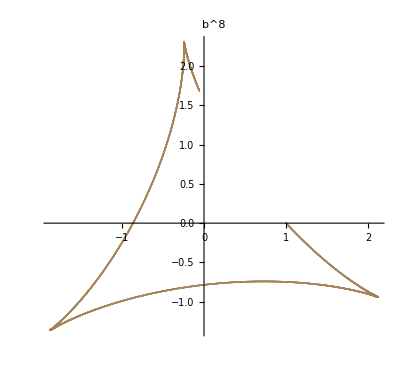

```mathematica
(* The relations b^3 central and b^9=Id for b turn clockwise, giving E^(4*Pi*I/3) at b^3, hence we lift to a relation B^3=z^-1, i.e., B^3*z *)
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[s*E^(4*Pi*I/3)]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^3 with ray to E^(4*Pi*I/3)"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^4"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^5"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^6"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^7"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^8"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xb].b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.b.z0).p3],ReIm[(MatrixExp[s*xb].b.b.b.b.b.b.b.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b^9 - full circle"]
```

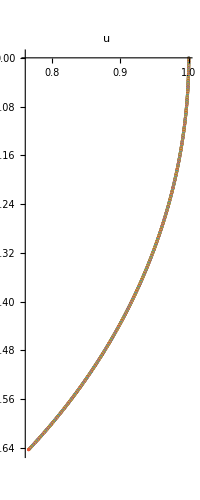

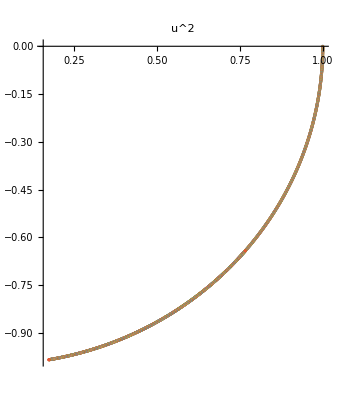

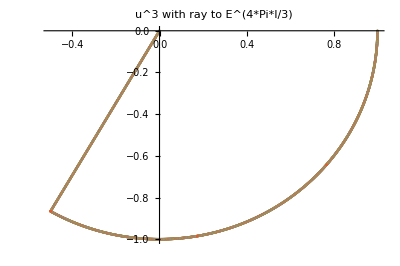

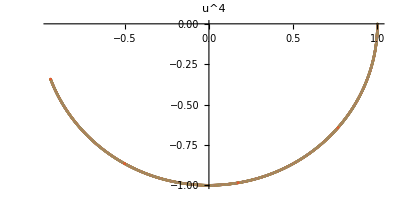

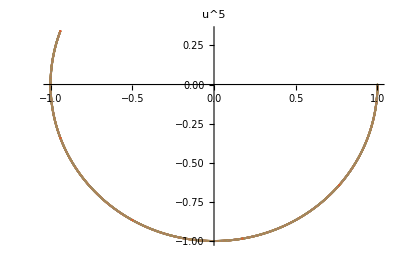

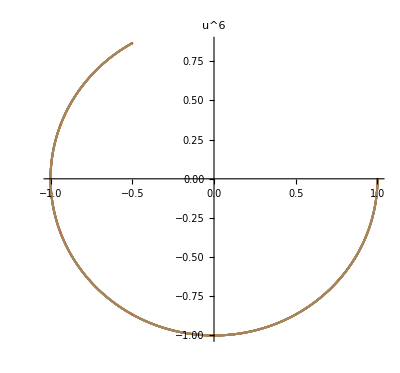

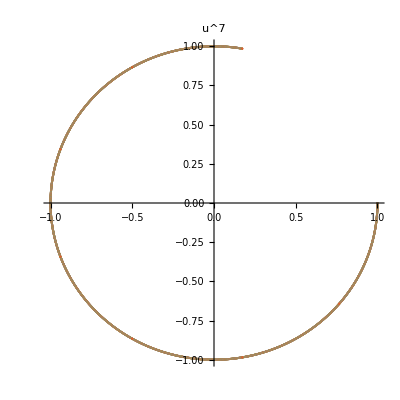

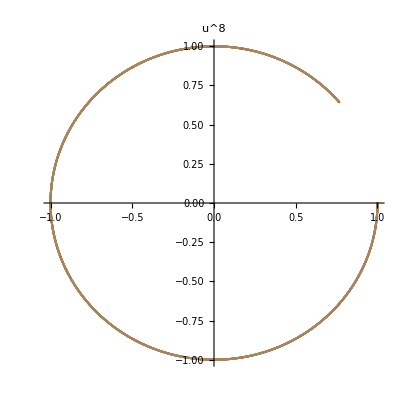

```mathematica
(* The relations u^3 central and u^9=Id for u turn clockwise, giving E^(4*Pi*I/3) at u^3, hence we lift to a relation U^3*z *)
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[s*E^(4*Pi*I/3)]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^3 with ray to E^(4*Pi*I/3)"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^4"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^5"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^6"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^7"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^8"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xu].u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.u.z0).p3],ReIm[(MatrixExp[s*xu].u.u.u.u.u.u.u.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u^9 - full circle"]
```

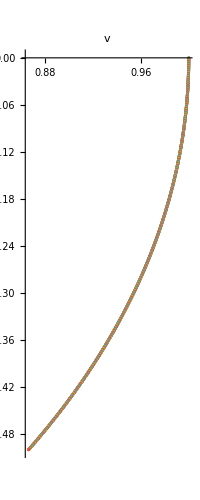

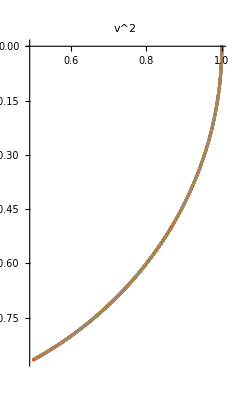

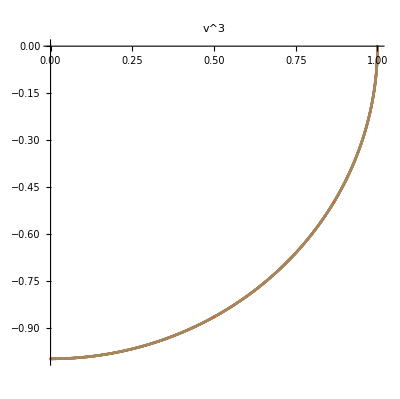

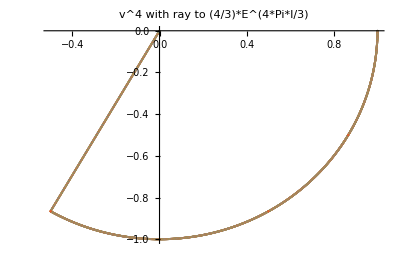

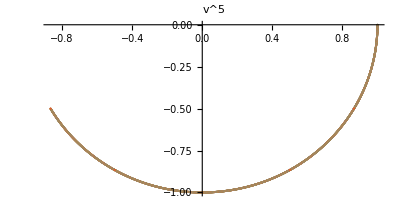

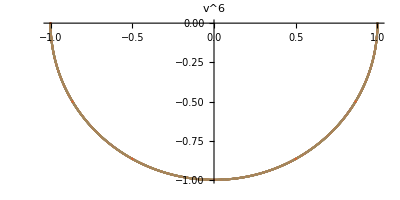

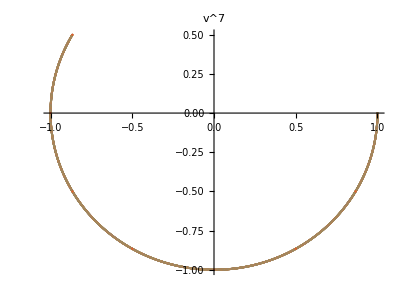

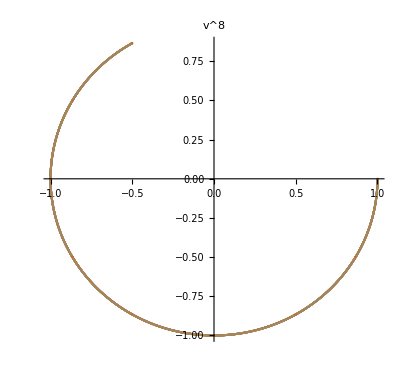

```mathematica
(* The relations v^4 central and v^12=Id for v turn clockwise, giving E^(4*Pi*I/3) at v^4, hence we lift to a relation V^4*z *)
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^3"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[s*E^(4*Pi*I/3)]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^4 with ray to (4/3)*E^(4*Pi*I/3)"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^5"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^6"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^7"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^8"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^9"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^10"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^11"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xv].v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.z0).p3],ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.z0).p3],
ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.z0).p3],
ReIm[(MatrixExp[s*xv].v.v.v.v.v.v.v.v.v.v.v.z0).p3]},
{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v^12 - full circle"]
```

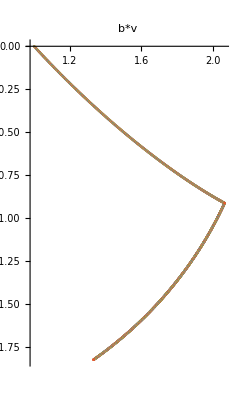

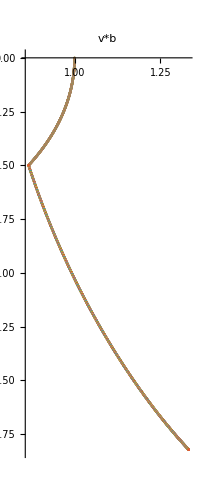

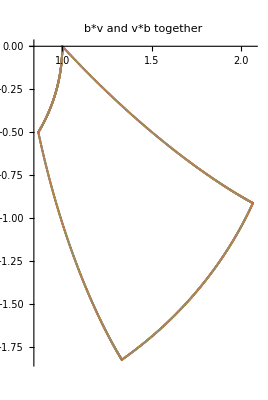

```mathematica
(* The relation b*v=v*b lifts to the universal cover, since the combined loop is nullhomotopic in C-{0} *)
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xv].b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xb].v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v*b"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xv].b.z0).p3],ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xb].v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*v and v*b together"]
```

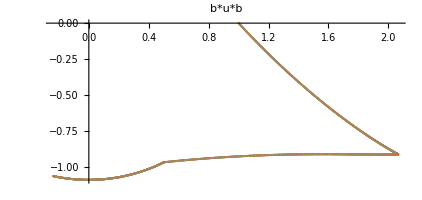

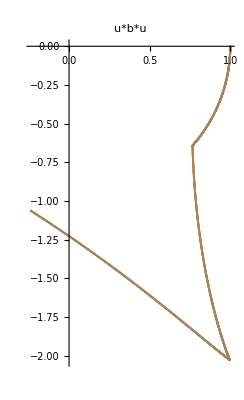

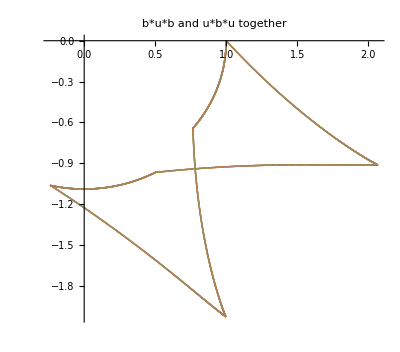

```mathematica
(* The relation b*u*b=u*b*u lifts to the universal cover, since the combined loop is nullhomotopic in C-{0} *)
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xu].b.z0).p3],ReIm[(MatrixExp[s*xb].u.b.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*u*b"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xb].u.z0).p3],ReIm[(MatrixExp[s*xu].b.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u*b*u"]
ListPlot[Table[{ReIm[(MatrixExp[s*xb].z0).p3],ReIm[(MatrixExp[s*xu].b.z0).p3],ReIm[(MatrixExp[s*xb].u.b.z0).p3],ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xb].u.z0).p3],ReIm[(MatrixExp[s*xu].b.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*u*b and u*b*u together"]
```

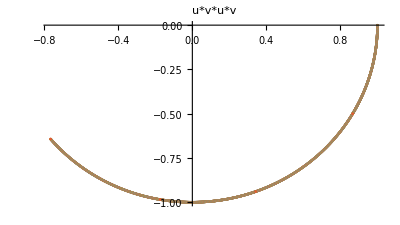

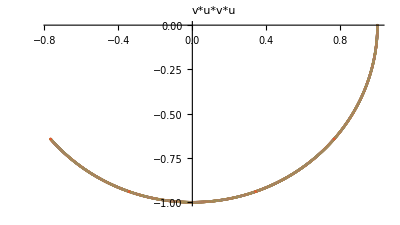

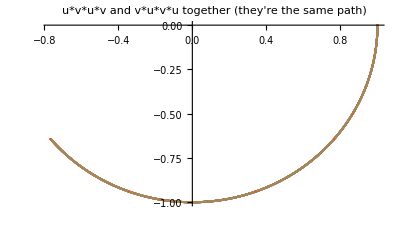

```mathematica
(* The relation u*v*u*v=v*u*v*ulifts to the universal cover, since the combined loop is nullhomotopic in C-{0} *)
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xv].u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u*v*u*v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xv].u.z0).p3],ReIm[(MatrixExp[s*xu].v.u.z0).p3],ReIm[(MatrixExp[s*xv].u.v.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"v*u*v*u"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xv].u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.u.v.z0).p3],ReIm[(MatrixExp[s*xu].z0).p3],ReIm[(MatrixExp[s*xv].u.z0).p3],ReIm[(MatrixExp[s*xu].v.u.z0).p3],ReIm[(MatrixExp[s*xv].u.v.u.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"u*v*u*v and v*u*v*u together (they're the same path)"]
```

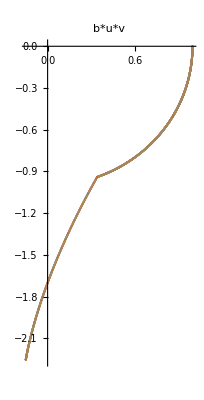

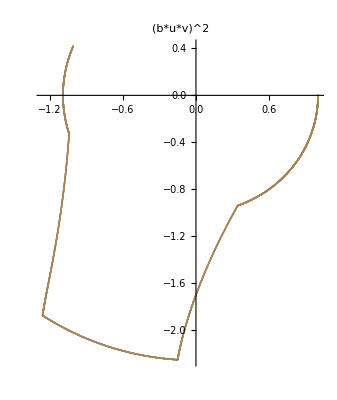

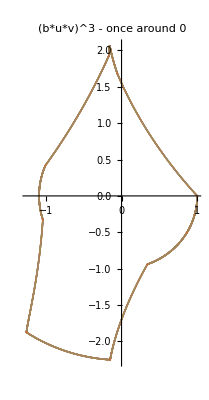

```mathematica
(* The relation (b*u*v)^3 rotations once around 0 in C-{0}, hence (B*U*V)^3 = z^-3 is the lifted relation *)
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"b*u*v"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.z0).p3],ReIm[(MatrixExp[s*xv].b.u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.b.u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"(b*u*v)^2"]
ListPlot[Table[{ReIm[(MatrixExp[s*xv].z0).p3],ReIm[(MatrixExp[s*xu].v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.z0).p3],ReIm[(MatrixExp[s*xv].b.u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xv].b.u.v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xu].v.b.u.v.b.u.v.z0).p3],ReIm[(MatrixExp[s*xb].u.v.b.u.v.b.u.v.z0).p3]},{s,0,1,0.001}],AspectRatio->Automatic,PlotLabel->"(b*u*v)^3 - once around 0"]
```